```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3=Real;
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
ts={35,50,65,80,95,110,125,140,155,170,180,200,215,220,230,240,245,260,275,280,290,300,305,320,335,340,350,360,365,380};
tssz=Dimensions[ts][[1]];
tfdistal=tfdistcu=Table[{},{k,1,tssz}];
tfmucu=tfmual=tfmpal=tfmpcu=Table[{0,0,0},{k,1,tssz}];
tsadd=PlusMinus[11.306,0.397];
maxsz=1000000;
Monitor[
For[i=1,i≤tssz,i++,
(*Print["Executing: ts = ",ts[[i]]," , i = ",i];*)
tfdistal[[i]]=ReadList[StringJoin[AscDir,seperator,"NStar",seperator,"aluminumElectrode",seperator,"tfSamples_",ToString[ts[[i]]],"sec.dat"],metaStructure3][[;;maxsz]];
tfdistcu[[i]]=ReadList[StringJoin[AscDir,seperator,"NStar",seperator,"copperElectrode",seperator,"tfSamples_",ToString[ts[[i]]],"sec.dat"],metaStructure3][[;;maxsz]];
(***)
tfmual[[i]]={Mean[tfdistal[[i]]],StandardDeviation[tfdistal[[i]]],MeanDeviation[tfdistal[[i]]]};
tfmucu[[i]]={Mean[tfdistcu[[i]]],StandardDeviation[tfdistcu[[i]]],MeanDeviation[tfdistcu[[i]]]};
medianal=Median[tfdistal[[i]]];
mediancu=Median[tfdistcu[[i]]];
tfmpal[[i]]={medianal,Sqrt[Total[(tfdistal[[i]]-medianal)^2/(Dimensions[tfdistal[[i]]][[1]]-1)]],MedianDeviation[tfdistal[[i]]]};
tfmpcu[[i]]={mediancu,Sqrt[Total[(tfdistcu[[i]]-mediancu)^2/(Dimensions[tfdistcu[[i]]][[1]]-1)]],MedianDeviation[tfdistcu[[i]]]};
];,ProgressIndicator[i/tssz,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

```mathematica
pttfmual=Table[{{ts[[k]]+2tsadd[[1]],2tsadd[[2]]},{tfmual[[k]][[1]],tfmpal[[k]][[3]]/2}},{k,1,tssz}];
pttfmucu=Table[{{ts[[k]]+2tsadd[[1]],2tsadd[[2]]},{tfmucu[[k]][[1]],tfmpcu[[k]][[3]]/2}},{k,1,tssz}];
pttfmpal=Table[{{ts[[k]]+2tsadd[[1]],2tsadd[[2]]},{tfmpal[[k]][[1]],tfmpal[[k]][[3]]/2}},{k,1,tssz}];
pttfmpcu=Table[{{ts[[k]]+2tsadd[[1]],2tsadd[[2]]},{tfmpcu[[k]][[1]],tfmpcu[[k]][[3]]/2}},{k,1,tssz}];
```

```mathematica
EDAListPlot[pttfmual,pttfmucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","<t_f>(s)"},PlotRange->{{35,420},{0.04,0.09}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
EDAListPlot[pttfmpal,pttfmpcu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","MPV[t_f](s)"},PlotRange->{{35,420},{0.03,0.08}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
```

-Graphics-

-Graphics-

```mathematica
icou=30;
histal=HistogramList[tfdistal[[icou]],{0,.31,.001}];
histalt=Transpose[{(histal[[1]][[;;-2]]+(histal[[1]][[2]]-histal[[1]][[2]])/2),histal[[2]][[;;]]}];
erral=Sqrt[histalt[[;;,2]]];
nlmal=NonlinearModelFit[histalt,d*PDF[SkewNormalDistribution[a,b,c],x],{a,b,c,d},x,Method->NMinimize];
Print["Chi^2/ndf, SkewGaussian: ",Total[((nlmal["FitResiduals"]/erral))^2]/(Dimensions[histalt][[1]]-2)];
nlmal["ParameterTable"]
nlmal["ANOVATable"]
nlmal2=LinearModelFit[histalt,Table[x^k,{k,0,20,1}],x];
Print["Chi^2/ndf, Polynomial-20th: ",Total[((nlmal2["FitResiduals"]/erral))^2]/(Dimensions[histalt][[1]]-2)];
nlmal2["ParameterTable"]
nlmal2["ANOVATable"]
(*Cu*)
histcu=HistogramList[tfdistcu[[icou]],{0,.31,.001}];
histcut=Transpose[{(histcu[[1]][[;;-2]]+(histcu[[1]][[2]]-histcu[[1]][[2]])/2),histcu[[2]][[;;]]}];
errcu=Sqrt[histcut[[;;,2]]];
nlmcu=NonlinearModelFit[histcut,d*PDF[SkewNormalDistribution[a,b,c],x],{a,b,c,d},x,Method->NMinimize];
Print["Chi^2/ndf, SkewGaussian: ",Total[((nlmcu["FitResiduals"]/errcu))^2]/(Dimensions[histcut][[1]]-2)];
nlmcu["ParameterTable"]
nlmcu["ANOVATable"]
nlmcu2=LinearModelFit[histcut,Table[x^k,{k,0,20,1}],x];
Print["Chi^2/ndf, Polynomial-20th: ",Total[((nlmcu2["FitResiduals"]/errcu))^2]/(Dimensions[histcut][[1]]-2)];
nlmcu2["ParameterTable"]
nlmcu2["ANOVATable"]
```

Chi^2/ndf, SkewGaussian: 268.238

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.010934 | 0.00080026 | 13.6631 | 1.66056×10^-33
b | 0.0599496 | 0.00126652 | 47.334 | 7.8012×10^-143
c | 2.66781 | 0.252974 | 10.5458 | 2.20054×10^-22
d | 976.375 | 12.6729 | 77.0446 | 2.00377×10^-202

| DF | SS | MS
Model | 4 | 6.92886×10^9 | 1.73222×10^9
Error | 306 | 1.67012×10^8 | 545789.
Uncorrected Total | 310 | 7.09587×10^9 | 
Corrected Total | 309 | 3.87254×10^9 |

Chi^2/ndf, Polynomial-20th: 7.22363

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5959.82 | 145.764 | 40.8869 | 3.55386×10^-122
x | -560165. | 129450. | -4.32726 | 0.0000208251
x^2 | 2.78917×10^8 | 3.77782×10^7 | 7.38303 | 1.65933×10^-12
x^3 | -4.5283×10^10 | 5.1427×10^9 | -8.80531 | 1.22561×10^-16
x^4 | 3.65571×10^12 | 3.98804×10^11 | 9.1667 | 9.39313×10^-18
x^5 | -1.74315×10^14 | 1.97239×10^13 | -8.83772 | 9.75659×10^-17
x^6 | 5.46748×10^15 | 6.67732×10^14 | 8.18814 | 8.60262×10^-15
x^7 | -1.20725×10^17 | 1.62222×10^16 | -7.442 | 1.14187×10^-12
x^8 | 1.96056×10^18 | 2.92238×10^17 | 6.70879 | 1.0331×10^-10
x^9 | -2.41016×10^19 | 3.99435×10^18 | -6.03393 | 4.89099×10^-9
x^10 | 2.28549×10^20 | 4.20794×10^19 | 5.43137 | 1.18761×10^-7
x^11 | -1.69128×10^21 | 3.45101×10^20 | -4.90083 | 1.59285×10^-6
x^12 | 9.82331×10^21 | 2.21431×10^21 | 4.43629 | 0.0000130256
x^13 | -4.48029×10^22 | 1.11175×10^22 | -4.02995 | 0.0000713991
x^14 | 1.5965×10^23 | 4.34541×10^22 | 3.67399 | 0.000284511
x^15 | -4.39354×10^23 | 1.30712×10^23 | -3.36124 | 0.00088038
x^16 | 9.14902×10^23 | 2.96518×10^23 | 3.08548 | 0.00222912
x^17 | -1.39326×10^24 | 4.9035×10^23 | -2.84135 | 0.00481177
x^18 | 1.46321×10^24 | 5.57553×10^23 | 2.62435 | 0.00914303
x^19 | -9.46886×10^23 | 3.8956×10^23 | -2.43065 | 0.01568
x^20 | 2.84487×10^23 | 1.26042×10^23 | 2.25708 | 0.0247499

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 2.80364×10^9 | 2.80364×10^9 | 100918. | 1.04352354859376×10^-369
x^2 | 1 | 2.58701×10^8 | 2.58701×10^8 | 9312.02 | 6.8007×10^-222
x^3 | 1 | 1.17119×10^8 | 1.17119×10^8 | 4215.74 | 2.13704×10^-174
x^4 | 1 | 3.50901×10^8 | 3.50901×10^8 | 12630.8 | 1.58239×10^-240
x^5 | 1 | 1.59827×10^8 | 1.59827×10^8 | 5753.02 | 7.95366×10^-193
x^6 | 1 | 4.19668×10^6 | 4.19668×10^6 | 151.061 | 3.25533×10^-28
x^7 | 1 | 2.88144×10^7 | 2.88144×10^7 | 1037.18 | 1.28116×10^-97
x^8 | 1 | 5.83909×10^7 | 5.83909×10^7 | 2101.8 | 1.25635×10^-134
x^9 | 1 | 3.52371×10^7 | 3.52371×10^7 | 1268.37 | 1.03371×10^-107
x^10 | 1 | 4.61226×10^6 | 4.61226×10^6 | 166.02 | 2.52258×10^-30
x^11 | 1 | 2.73191×10^6 | 2.73191×10^6 | 98.3362 | 3.85066×10^-20
x^12 | 1 | 1.43585×10^7 | 1.43585×10^7 | 516.84 | 2.59123×10^-66
x^13 | 1 | 1.36596×10^7 | 1.36596×10^7 | 491.683 | 2.55739×10^-64
x^14 | 1 | 5.10664×10^6 | 5.10664×10^6 | 183.815 | 9.56736×10^-33
x^15 | 1 | 314575. | 314575. | 11.3232 | 0.000868926
x^16 | 1 | 594136. | 594136. | 21.3861 | 5.67031×10^-6
x^17 | 1 | 2.34302×10^6 | 2.34302×10^6 | 84.3377 | 8.32144×10^-18
x^18 | 1 | 2.47723×10^6 | 2.47723×10^6 | 89.1686 | 1.27152×10^-18
x^19 | 1 | 1.34549×10^6 | 1.34549×10^6 | 48.4312 | 2.29677×10^-11
x^20 | 1 | 143139. | 143139. | 5.15232 | 0.0239518
Error | 289 | 8.02882×10^6 | 27781.4 |  | 
Total | 309 | 3.87254×10^9 |  |  |

Chi^2/ndf, SkewGaussian: 262.993

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0112861 | 0.000832553 | 13.556 | 4.13609×10^-33
b | 0.0621224 | 0.00131562 | 47.2193 | 1.49929×10^-142
c | 2.65983 | 0.253175 | 10.5059 | 3.00374×10^-22
d | 978.678 | 12.7392 | 76.8242 | 4.61213×10^-202

| DF | SS | MS
Model | 4 | 6.71189×10^9 | 1.67797×10^9
Error | 306 | 1.61897×10^8 | 529076.
Uncorrected Total | 310 | 6.87379×10^9 | 
Corrected Total | 309 | 3.65086×10^9 |

Chi^2/ndf, Polynomial-20th: 8.14229

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5638.6 | 144.684 | 38.9719 | 4.46581×10^-117
x | -316768. | 128491. | -2.46528 | 0.0142717
x^2 | 1.81987×10^8 | 3.74983×10^7 | 4.85321 | 1.9906×10^-6
x^3 | -2.93289×10^10 | 5.1046×10^9 | -5.74558 | 2.32163×10^-8
x^4 | 2.26965×10^12 | 3.95849×10^11 | 5.73362 | 2.47356×10^-8
x^5 | -1.01632×10^14 | 1.95778×10^13 | -5.19116 | 3.94605×10^-7
x^6 | 2.94978×10^15 | 6.62785×10^14 | 4.45058 | 0.0000122404
x^7 | -5.94952×10^16 | 1.6102×10^16 | -3.6949 | 0.000263059
x^8 | 8.70861×10^17 | 2.90073×10^17 | 3.00221 | 0.00291442
x^9 | -9.50265×10^18 | 3.96476×10^18 | -2.39678 | 0.0171753
x^10 | 7.84829×10^19 | 4.17677×10^19 | 1.87903 | 0.0612461
x^11 | -4.9339×10^20 | 3.42544×10^20 | -1.44037 | 0.150845
x^12 | 2.35113×10^21 | 2.1979×10^21 | 1.06971 | 0.285641
x^13 | -8.34559×10^21 | 1.10351×10^22 | -0.756276 | 0.4501
x^14 | 2.11573×10^22 | 4.31321×10^22 | 0.490522 | 0.624137
x^15 | -3.43025×10^22 | 1.29743×10^23 | -0.264387 | 0.79167
x^16 | 2.09518×10^22 | 2.94322×10^23 | 0.0711867 | 0.943298
x^17 | 4.60261×10^22 | 4.86718×10^23 | 0.0945643 | 0.924726
x^18 | -1.31357×10^23 | 5.53423×10^23 | -0.237353 | 0.812551
x^19 | 1.39532×10^23 | 3.86674×10^23 | 0.360851 | 0.718474
x^20 | -5.85596×10^22 | 1.25109×10^23 | -0.46807 | 0.640087

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 2.66636×10^9 | 2.66636×10^9 | 97414.5 | 1.69621872403476×10^-367
x^2 | 1 | 2.03346×10^8 | 2.03346×10^8 | 7429.17 | 3.41406×10^-208
x^3 | 1 | 1.37141×10^8 | 1.37141×10^8 | 5010.4 | 1.35561×10^-184
x^4 | 1 | 3.39589×10^8 | 3.39589×10^8 | 12406.8 | 1.98176×10^-239
x^5 | 1 | 1.33001×10^8 | 1.33001×10^8 | 4859.14 | 8.90794×10^-183
x^6 | 1 | 774863. | 774863. | 28.3094 | 2.07616×10^-7
x^7 | 1 | 3.5425×10^7 | 3.5425×10^7 | 1294.24 | 9.54423×10^-109
x^8 | 1 | 5.64025×10^7 | 5.64025×10^7 | 2060.64 | 1.54639×10^-133
x^9 | 1 | 2.7762×10^7 | 2.7762×10^7 | 1014.28 | 1.59263×10^-96
x^10 | 1 | 1.68361×10^6 | 1.68361×10^6 | 61.51 | 8.56582×10^-14
x^11 | 1 | 5.46126×10^6 | 5.46126×10^6 | 199.525 | 8.29852×10^-35
x^12 | 1 | 1.62956×10^7 | 1.62956×10^7 | 595.355 | 3.70278×10^-72
x^13 | 1 | 1.15322×10^7 | 1.15322×10^7 | 421.327 | 2.22621×10^-58
x^14 | 1 | 2.70005×10^6 | 2.70005×10^6 | 98.6455 | 3.42725×10^-20
x^15 | 1 | 209.7 | 209.7 | 0.00766131 | 0.930312
x^16 | 1 | 1.08126×10^6 | 1.08126×10^6 | 39.5033 | 1.20365×10^-9
x^17 | 1 | 2.25386×10^6 | 2.25386×10^6 | 82.344 | 1.82033×10^-17
x^18 | 1 | 1.64095×10^6 | 1.64095×10^6 | 59.9517 | 1.64752×10^-13
x^19 | 1 | 500952. | 500952. | 18.3021 | 0.0000256538
x^20 | 1 | 5369.12 | 5369.12 | 0.196159 | 0.658171
Error | 289 | 7.91029×10^6 | 27371.3 |  | 
Total | 309 | 3.65086×10^9 |  |  |

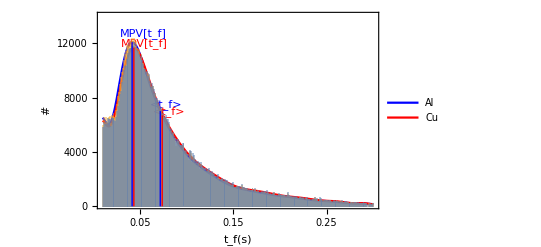

```mathematica
icou=30;
lineStyle1={Thick,Blue};
line11=Line[{{tfmual[[icou]][[1]],0},{tfmual[[icou]][[1]],nlmal2[tfmual[[icou]][[1]]]}}];
line12=Line[{{x/.FindMaximum[nlmal2[x],{x,.02,.3}][[2]],0},{x/.FindMaximum[nlmal2[x],{x,.02,.3}][[2]],FindMaximum[nlmal2[x],{x,.02,.3}][[1]]}}];
lineStyle2={Thick,Red};
line21=Line[{{tfmucu[[icou]][[1]],0},{tfmucu[[icou]][[1]],nlmal2[tfmucu[[icou]][[1]]]}}];
line22=Line[{{x/.FindMaximum[nlmcu2[x],{x,.02,.3}][[2]],0},{x/.FindMaximum[nlmcu2[x],{x,.02,.3}][[2]],FindMaximum[nlmcu2[x],{x,.02,.3}][[1]]}}];
text={Thick,Black};
Show[{
Plot[{nlmal2[x],nlmcu2[x]},{x,0.01,.3},PlotRange->{{0.01,.3},{100,14000}},PlotLegends->{"Al","Cu"},Frame->True,FrameLabel->{"t_f(s)","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotStyle->{{Thick,Blue},{Thick,Red}},
Epilog->{
{Directive[lineStyle1],line11,line12,Style[Text["MPV[t_f]",{.053,12750}],Large],Style[Text["<t_f>",{.078,7500}],Large]},
{Directive[lineStyle2],line21,line22,Style[Text["MPV[t_f]",{.055,12000}],Large],Style[Text["<t_f>",{.081,7000}],Large]}
}],
Histogram[{tfdistal[[icou]],tfdistcu[[icou]]},{0.01,.3,.001},PlotRange->{{0.01,.3},{100,14000}}]
}]
```

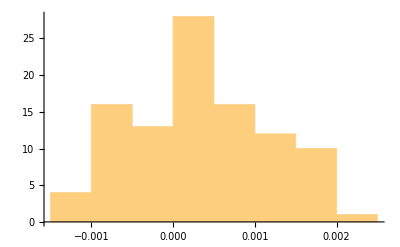

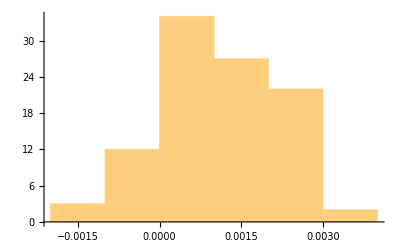

{0.19,Null}

{0.194198,Null}

{0.185254,Null}

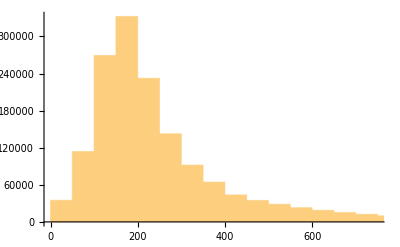

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz3=100;
maxsz2=100000;
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
Histogram[ab]
(*eb=RandomVariate[NormalDistribution[-.001,.0001],maxsz3];*)
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]],maxsz3];
Histogram[eb]
tftseb0=Flatten[KroneckerProduct[-1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tfdistcu[[icou]][[;;maxsz2]]]];//AbsoluteTiming
tftsab=Flatten[KroneckerProduct[-1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tfdistcu[[icou]][[;;maxsz2]]]];//AbsoluteTiming
tftseb=Flatten[KroneckerProduct[-1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tfdistcu[[icou]][[;;maxsz2]]]];//AbsoluteTiming
Histogram[Sqrt[tftseb0]]
(*
ab=-Select[RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3],#<0&];
Histogram[ab]
eb=-Select[RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]],maxsz3],#<0&];
Histogram[eb]
maxsz2=100000;
tftseb0=Flatten[KroneckerProduct[Sqrt[1/eb],Sqrt[(descdat[[i]][[7]]+2tsadd[[1]])*tfdistcu[[icou]][[;;maxsz2]]]]];//AbsoluteTiming
tftsab=Flatten[KroneckerProduct[Sqrt[1/ab],Sqrt[(descdat[[i]][[7]]+2tsadd[[1]])/tfdistcu[[icou]][[;;maxsz2]]]]];//AbsoluteTiming
tftseb=Flatten[KroneckerProduct[Sqrt[1/eb],Sqrt[(descdat[[i]][[7]]+2tsadd[[1]])/tfdistcu[[icou]][[;;maxsz2]]]]];//AbsoluteTiming
*)
```

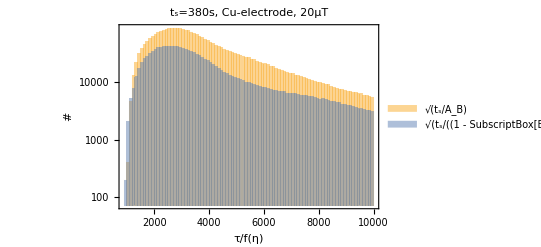

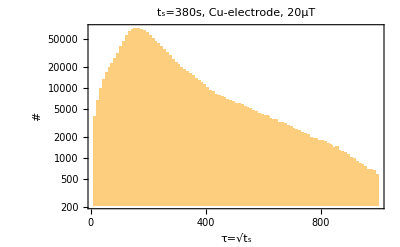

```mathematica
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
endpt=10000;
Histogram[{Sqrt[tftsab],Sqrt[tftseb]},{0,endpt,100},PlotRange->{{1000,endpt},{0,500000}},ChartLegends->{"√(t_s/A_B)","√(t_s/((1 - SubscriptBox[E, B])·SubscriptBox[t, f]))"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},Frame->True,FrameLabel->{"τ/f(η)","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[Sqrt[tftseb0],{10,endpt/10,10},PlotRange->{{10,endpt/10},Automatic},Frame->True,FrameLabel->{"τ=√t_s","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],None},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
```

99.9

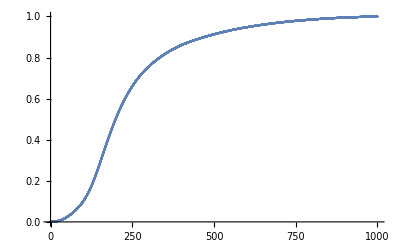

```mathematica
histtftseb0=HistogramList[Sqrt[tftseb0],{0,1000,.1}];
histtftseb0t=Transpose[{(histtftseb0[[1]][[;;-2]]+(histtftseb0[[1]][[2]]-histtftseb0[[1]][[2]])/2),histtftseb0[[2]][[;;]]}];
histhisttftseb0tot=Total[histtftseb0t[[;;,2]]];
cumhisttftseb0t=ParallelTable[{histtftseb0t[[k]][[1]],Total[histtftseb0t[[;;k,2]]]/histhisttftseb0tot},{k,1,Dimensions[histtftseb0t][[1]]}];
val=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val]][[1]]]][[1]]
ListPlot[cumhisttftseb0t,PlotRange->{{0,1000},{0,1}}]
```

```mathematica
val=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val]][[1]]]][[1]]
Sqrt[pttfmucu[[-1]][[2]][[1]]*pttfmucu[[-1]][[1]][[1]]/.00100883]
```

99.9

171.514

## Tests

```mathematica
Print["Al"];
Print["<t_f>, mean: ",Mean[tfdistal[[icou]]]," ± ",StandardDeviation[tfdistal[[icou]]]," , ",MeanDeviation[tfdistal[[icou]]]];
Print["<t_f>, median: ",medianal=Median[tfdistal[[icou]]]," ± ",Sqrt[Total[(tfdistal[[icou]]-medianal)^2/(Dimensions[tfdistal[[icou]]][[1]]-1)]]," , ",MedianDeviation[tfdistal[[icou]]]];
Print["Cu"];
Print["<t_f>, mean: ",Mean[tfdistcu[[icou]]]," ± ",StandardDeviation[tfdistcu[[icou]]]," , ",MeanDeviation[tfdistcu[[icou]]]];
Print["<t_f>, median: ",mediancu=Median[tfdistcu[[icou]]]," ± ",Sqrt[Total[(tfdistcu[[icou]]-mediancu)^2/(Dimensions[tfdistcu[[icou]]][[1]]-1)]]," , ",MedianDeviation[tfdistcu[[icou]]]];
```

Al

<t_f>, mean: 0.0716322 ± 0.0556141 , 0.0414921

<t_f>, median: 0.056531 ± 0.0576279 , 0.0265802

Cu

<t_f>, mean: 0.0737107 ± 0.0566225 , 0.0424735

<t_f>, median: 0.0584172 ± 0.0586515 , 0.0274539

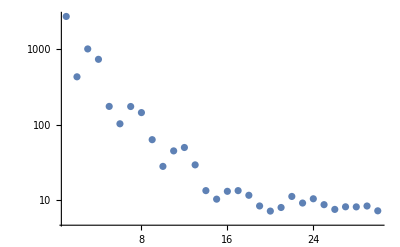

```mathematica
nmax=30;
chi2sat=Table[0,{k,1,nmax}];
For[i=1,i≤nmax,i++,
nlmal2=LinearModelFit[histalt,Table[x^k,{k,0,i,1}],x];
chi2sat[[i]]=Total[((nlmal2["FitResiduals"]/erral))^2]/(Dimensions[histalt][[1]]-2);
];
ListLogPlot[chi2sat,PlotRange->Full]
```

```mathematica
Times[{a,b},{c,d}]
fitsize=100000;
aa=Symbol["a"<>ToString[#]]&/@Range[fitsize];
bb=Symbol["b"<>ToString[#]]&/@Range[100];
Flatten[Outer[Times,aa,bb]];//AbsoluteTiming
Flatten[KroneckerProduct[aa,bb]];//AbsoluteTiming
```

{a c,b d}

{33.5961,Null}

{20.5569,Null}

### 200k samples

{18.2501,Null}

{9.26383,Null}

### 100k samples

{8.46109,Null}

{4.95156,Null}

```mathematica
(*descdattf=MapThread[Append,{MapThread[Append,{MapThread[Append,{MapThread[Append,{descdat,tf}],tferr}],tf2}],tf2err}];
EDAListPlot[pttfal,Joined->True,Frame->True,FrameLabel->{"t_s(s)","t_f(s)"},PlotRange->{{20,390},{0.05,.1}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]*)
```

### With 1k samples

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0100679 | 0.00253126 | 3.97742 | 0.0000864236
b | 0.0928409 | 0.00430418 | 21.5699 | 4.48836×10^-64
c | 3.62752 | 0.913818 | 3.96963 | 0.0000891586
d | 1.01843 | 0.0349999 | 29.098 | 2.12417×10^-91

| DF | SS | MS
Model | 4 | 5179.26 | 1294.81
Error | 316 | 876.743 | 2.7745
Uncorrected Total | 320 | 6056. | 
Corrected Total | 319 | 2931. |

### With 10k samples

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00727394 | 0.00121926 | 5.96588 | 6.51874×10^-9
b | 0.10595 | 0.00193271 | 54.8192 | 1.82117×10^-163
c | 3.79249 | 0.423439 | 8.9564 | 2.95438×10^-17
d | 10.447 | 0.155939 | 66.9942 | 8.32729×10^-189

| DF | SS | MS
Model | 4 | 478508. | 119627.
Error | 316 | 13019.5 | 41.201
Uncorrected Total | 320 | 491528. | 
Corrected Total | 319 | 179028. |

### With 250k samples

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00904747 | 0.000723837 | 12.4993 | 2.10428×10^-29
b | 0.106458 | 0.00114447 | 93.0202 | 1.19754×10^-231
c | 3.17037 | 0.191105 | 16.5896 | 6.77437×10^-45
d | 2642.46 | 21.9088 | 120.612 | 2.58879×10^-266

| DF | SS | MS
Model | 4 | 2.93591×10^10 | 7.33976×10^9
Error | 316 | 2.32635×10^8 | 736185.
Uncorrected Total | 320 | 2.95917×10^10 | 
Corrected Total | 319 | 1.00604×10^10 |